## Square Well - 4 lowest Odd parity levels

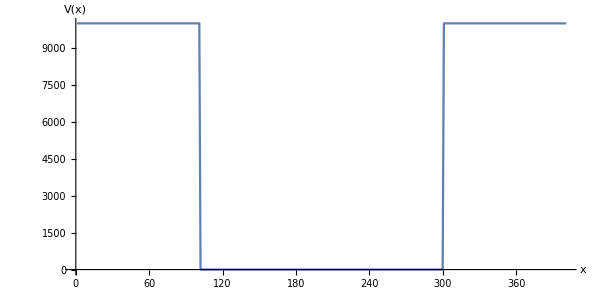

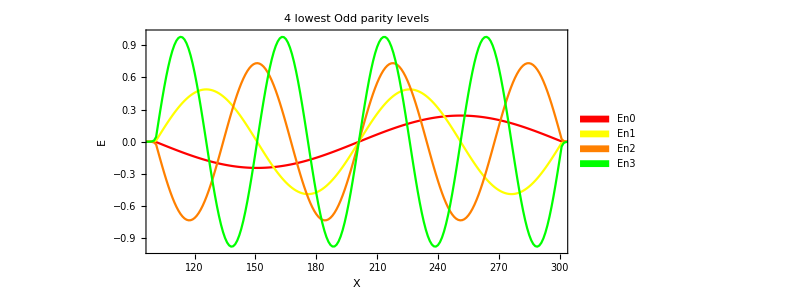

The exact Energies for the first 5 odd levels are:
 {4.9348, 19.7392, 44.4132, 78.9568, 123.37}While the estimated values from my computations using the shooting method were:
{4.89847, 19.5891, 44.0575, 78.2796, 122.222}

```mathematica
ClearAll["Global`*"]
xMax = 2.0; dx = 0.01; 
x = Range[-xMax, xMax, dx]; lx = Length[x];
v = Table[0.0, {i,lx}];
potEng = 10000.0;
Do[
If[x[[i]]<= -1.0, v[[i]] = potEng];
If[x[[i]]>= 1.0, v[[i]] = potEng];
If[x[[i]]== 0.0,i0 = i]; (* i0 = central position of the well *)
,{i,lx}];
nEng = 5; (* number of energy levels *)
color={Red,Yellow,Orange,Green,Magenta};
labels={"En0","En1","En2","En3","En4"};
engOddList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = 1.0; (* first guess for E *)
psiMax = 2.0; (* top bound for psi *)

Do[
dE = .4; (* first guess for dE *) 

(* Obtaining the sign of the initial psi RIGHT*)
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx*j;  (* δx slop at x = 0 and 0.0 ψ at x=0*)
i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLastR=psi[[i-1]] ; (* Last value of psi before quitting *)

(* Main loop for energy levels *)
While[Abs[dE] >0.000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx*j; psi[[i0 +1]] = dx*j;  (* δx slop at x = 0 and 0.0 ψ at x=0*)

(*I'll multiply dx by J as a means of systematically increasing the slope of ψ around x=0 with higher E values, to accomodate higher slopes for increasing E values and avoid the probability amplitudes falling off with larger E's as the frequncies increase*)

i=i0+2;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng + dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng + dE];
psiLastR = psiNewR];
(*-------------------------------------------------------------------------------------------*)

dEl=0.4;
While[Abs[dEl] > 0.000000000001,
k=i0-2;
While[Abs[psi[[k+1]]] < psiMax && k > 0,
psi[[k]] = 2.0 psi[[k+1]] - psi[[k+2]] - 2.0 (eng - v[[k+1]])psi[[k+1]] dx^2;  k--];
psiNewL=psi[[k+1]] ;
If[Sign[psiNewL] == Sign[psiLastL], eng = eng - dEl]; (*used negative here to reverse direction*)
If[Sign[psiNewL] != Sign[psiLastL],dEl=-dEl/2.0; eng = eng + dEl];
psiLastL = psiNewL];

(*-------------------------------------------------------------------------------------------*)
engOddList[[j]] = eng;
eng = eng + 0.5;

(*I'll divide ψ by 0.328, which is the amplitude I got before normalization*)

plot[[j]]=ListLinePlot[psi/0.328*j/2^2,PlotRange->All,PlotStyle->{color[[j]],PointSize->0.005},PlotLegends->SwatchLegend[{color[[j]]},{labels[[j]]}]]
,{j,nEng}];

(* Results *)
leg=SwatchLegend[{Red,Yellow,Orange},{"E0","E1","E2"}];
engOddList (* Calculations using shooting method *);
engExact =Table[((2.0n ) Pi/2.0)^2/2.0,{n,5}] ;(* Exact .. I corrected it since the odd functions have different integers or half integers of pi in their equation*)
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.5,ImageSize->600]
Show[plot[[1]],plot[[2]],plot[[3]],plot[[4]],PlotRange->{{100,300},{-1,1}},AspectRatio->0.5,ImageSize->600,Frame -> True, FrameLabel->{Style["X",FontSize->15],Style["E",FontSize->20]},PlotLabel->"4 lowest Odd parity levels"]

Print["The exact Energies for the first 5 odd levels are:\n " <>ToString [engExact]<>"While the estimated values from my computations using the shooting method were:\n" <>ToString[engOddList]]
```